```mathematica
fuck=Table[Integrate[Exp[I*t*s]*ChebyshevT[k,t],{t,-1,1}],{k,0,5}]
```

{(2 Sin[s])/s,(2 ⅈ (-s Cos[s]+Sin[s]))/s^2,(8 s Cos[s]+2 (-4+s^2) Sin[s])/s^3,-(2 ⅈ (s (-24+s^2) Cos[s]+3 (8-3 s^2) Sin[s]))/s^4,(32 s (-12+s^2) Cos[s]+2 (192-80 s^2+s^4) Sin[s])/s^5,-(2 ⅈ (s (1920-200 s^2+s^4) Cos[s]-5 (384-168 s^2+5 s^4) Sin[s]))/s^6}

```mathematica
fuck
```

{(2 Sin[s])/s,(2 ⅈ (-s Cos[s]+Sin[s]))/s^2,(8 s Cos[s]+2 (-4+s^2) Sin[s])/s^3,-(2 ⅈ (s (-24+s^2) Cos[s]+3 (8-3 s^2) Sin[s]))/s^4,(32 s (-12+s^2) Cos[s]+2 (192-80 s^2+s^4) Sin[s])/s^5,-(2 ⅈ (s (1920-200 s^2+s^4) Cos[s]-5 (384-168 s^2+5 s^4) Sin[s]))/s^6}

```mathematica
fuck
```

{(2 Sin[s])/s,(2 ⅈ (-s Cos[s]+Sin[s]))/s^2,(8 s Cos[s]+2 (-4+s^2) Sin[s])/s^3,-(2 ⅈ (s (-24+s^2) Cos[s]+3 (8-3 s^2) Sin[s]))/s^4,(32 s (-12+s^2) Cos[s]+2 (192-80 s^2+s^4) Sin[s])/s^5,-(2 ⅈ (s (1920-200 s^2+s^4) Cos[s]-5 (384-168 s^2+5 s^4) Sin[s]))/s^6}

```mathematica
fuck
```

{(2 Sin[s])/s,(2 ⅈ (-s Cos[s]+Sin[s]))/s^2,(8 s Cos[s]+2 (-4+s^2) Sin[s])/s^3,-(2 ⅈ (s (-24+s^2) Cos[s]+3 (8-3 s^2) Sin[s]))/s^4,(32 s (-12+s^2) Cos[s]+2 (192-80 s^2+s^4) Sin[s])/s^5,-(2 ⅈ (s (1920-200 s^2+s^4) Cos[s]-5 (384-168 s^2+5 s^4) Sin[s]))/s^6}

```mathematica
fuck[[1]]
```

(2 Sin[s])/s

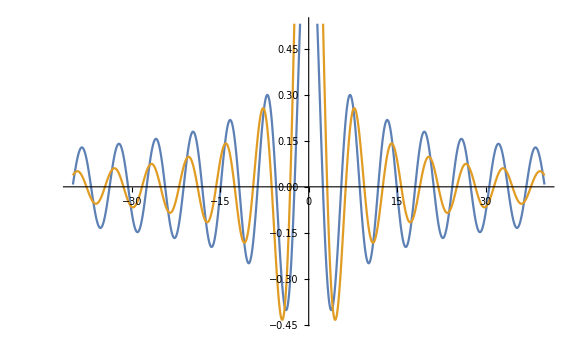

```mathematica
Plot[{BesselJ[0,s],Re[fuck[[1]]]},{s,-40,40}]
```

```mathematica
Integrate[Exp[I*x*y]/Sqrt[1-x^2],{x,-1,1}]
```

π BesselJ[0,y]

```mathematica
Integrate[fuck[[1]]*fuck[[3]]*BesselJ[0,s],{s,0,Infinity}]
```

1/27 ((24 √2 (507+293 √3))/(7+4 √3)^(7/4)-9 π-1/(7+4 √3)^(7/4)(2-√3)^(1/4) ((26+15 √3)^(3/4) (903 √2+666 √6)-48 (-1152-670 √3-30 √(2+√3) (7+4 √3)^(3/4)+75 √(3 (2+√3)) (7+4 √3)^(3/4)) Hypergeometric2F1[-1/4,-1/4,3/4,1/4 (2-√3)]-39904 Hypergeometric2F1[-1/4,3/4,7/4,1/4 (2-√3)]-23328 √3 Hypergeometric2F1[-1/4,3/4,7/4,1/4 (2-√3)]-3840 √(2+√3) (7+4 √3)^(3/4) Hypergeometric2F1[-1/4,3/4,7/4,1/4 (2-√3)]+3240 √(3 (2+√3)) (7+4 √3)^(3/4) Hypergeometric2F1[-1/4,3/4,7/4,1/4 (2-√3)]+5680 Hypergeometric2F1[3/4,3/4,7/4,1/2-(√3)/4]+3280 √3 Hypergeometric2F1[3/4,3/4,7/4,1/2-(√3)/4]+36 √(2+√3) (7+4 √3)^(3/4) Hypergeometric2F1[3/4,3/4,7/4,1/2-(√3)/4]+18 √(3 (2+√3)) (7+4 √3)^(3/4) Hypergeometric2F1[3/4,3/4,7/4,1/2-(√3)/4])-18 (2 ArcCot[1-√2 (7+4 √3)^(1/4)]-2 ArcCot[1+√2 (7+4 √3)^(1/4)]+Log[1-√2 (7-4 √3)^(1/4)+√(7-4 √3)]-Log[1+√2 (7-4 √3)^(1/4)+√(7-4 √3)]))